## Diffusion in Two Dimensions — Steady State

## Completed and Analyzed in class, April 18, 2025

This is our twenty-first notebook. In the twentieth notebook, we did one-dimensional diffusion. Now we are graduating to two-dimensional diffusion. Here is an example:

-Graphics-

NB: This is a two-dimensional problem, not a three-dimensional one. The third dimension in the plot is just helping to visualize the temperature, and unless you are red-green colorblind, the information supplied by displaying a third dimension is redundant.

The problem has the type of equation that we are currently studying. The specifics of this problem is that it is a two-dimensional plate that has alternating regions of hot and cold along one side, and is at an intermediate temperature along the other three sides. For more, see: https://youtu.be/2aJ3fFwET68.

We are going to specify the equation on the interior, and then the boundary conditions, and Mathematica is going to figure out the steady-state solution.

If you want to see more of the wide variety of equations that can be solved using the techniques we are using, try https://www.cfm.brown.edu/people/dobrush/am34/Mathematica/ch6/parabolic.html.

### Two-Dimensional Diffusion — Steady-State Theory

In one dimension, we had:

c(T,x) dT/dt=σ(x)(d^2 T)/(d x^2)

The obvious generalization (I won’t bore you with yet another derivation of combinations of second derivatives) to two dimensions is:

c(T,x,y) dT/dt=σ(x,y)((d^2 T)/(d x^2)+(d^2 T)/(d y^2))

It can be very interesting to see the time-dependent way that the system settles down to equilibrium, but now I want to make a huge simplification, which is that the system has already settled down to equilibrium.

As long as the external sources of heat are supplied in a steady (unchanging) way, the system will eventually settle down. Once it settles down, dT/dt=0, and this is true everywhere in x and y. So for the steady state, our equations become:

0=σ(x,y)((d^2 T)/(d x^2)+(d^2 T)/(d y^2))

and T, whatever it is, is unchanging, and so it is no longer a function of t. It is only a function of x and y. Also, even if We just have this as what we specify to Mathematica:

```mathematica
Module[{sigma=1},{ sigma (Derivative[2,0][temp][x,y]+Derivative[0,2][temp][x,y])==0}] // TraditionalForm
```

{temp^(0,2)(x,y)+temp^(2,0)(x,y)==0}

### Adding the Boundary Conditions

Let’s make boundary conditions like the one pictured at the beginning of this notebook:

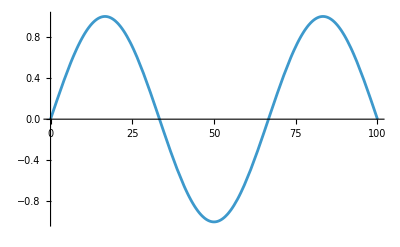

```mathematica
lengthX=100;
lengthY=60;
amplitude=1;

mode=3;
f[x_]:=amplitude Sin[mode Pi x/lengthX]
Plot[f[x],{x,0,lengthX}]
```

So here is our problem but now with the boundary conditions added:

```mathematica
Module[{sigma=1},{sigma (Derivative[2,0][temp][x,y]+Derivative[0,2][temp][x,y])==0,temp[x,0]==f[x],temp[x,lengthY]==0,temp[0,y]==0,temp[lengthX,y]==0}]  // TraditionalForm
```

{temp^(0,2)(x,y)+temp^(2,0)(x,y)==0,temp(x,0)==sin((3 π x)/100),temp(x,60)==0,temp(0,y)==0,temp(100,y)==0}

### No Initial Conditions!

This is a steady-state problem. Time is not involved. We do not need to specify any initial conditions. That means the whole problem is what we already specified in the previous section:

```mathematica
twoDimensionalDiffusionProblem=Module[{sigma=1},{ sigma (Derivative[2,0][temp][x,y]+Derivative[0,2][temp][x,y])==0,temp[x,0]==f[x],temp[x,lengthY]==0,temp[0,y]==0,temp[lengthX,y]==0}]
```

{temp^(0,2)[x,y]+temp^(2,0)[x,y]==0,temp[x,0]==Sin[(3 π x)/100],temp[x,60]==0,temp[0,y]==0,temp[100,y]==0}

### A Great Trick — Known as “Separation of Variables”

We guess that T(x,y)=u(x)v(y).

Upon putting this guess into the differential equations, we discover that if this trick is to work, then u(x) must satisfy the ordinary differential equation:

(d^2 u)/(d x^2)=-λ u

and the solutions that have u(0)=0 and u(l_x)=0 are

u_n(x)=sin nπx/l_x, with n=1, 2, 3, ...

and λ_n=(n^2 π^2)/l_x^2

Now that we know the possible u_n(x) and λ_n, we put those into the v equation which is

(d^2 v)/(d y^2)=λ v

and which has the solutions

v(y)=c_+e^(√λ_n y)+c_-e^(-√λ_ny)

If this solution is to be zero at l_y, we must have

0=c_+e^(√λ_n l_y)+c_-e^(-√λ_n l_y)

If the full solution is to be sin(3πx)/l_x at y=0 that tells us we must have the solutions with u_3(x) and λ_3 and that

 1=c_++c_- 

So

0=c_+e^(√λ_n l_y)+(1-c_+)e^(-√λ_n l_y)=c_+(e^(√λ_n l_y)-e^(-√λ_n l_y))+e^(-√λ_n l_y)

So

c_+=-e^(-√λ_n l_y)/(e^(√λ_n l_y)-e^(-√λ_n l_y))

and

c_-=1-c_+=1--e^(-√λ_n l_y)/(e^(√λ_n l_y)-e^(-√λ_n l_y))=e^(√λ_n l_y)/(e^(√λ_n l_y)-e^(-√λ_n l_y))

So

v(y)=c_+e^(√λ_n y)+c_-e^(-√λ_ny)=-e^(-√λ_n l_y)/(e^(√λ_n l_y)-e^(-√λ_n l_y))e^(√λ_n y)+e^(√λ_n l_y)/(e^(√λ_n l_y)-e^(-√λ_n l_y))e^(-√λ_ny)

Stick in from what we learned solving the u(x) equation, that we must λ_3^2=(3π)/l_x, and we then have

v(y)=-e^(-(3π)/l_x l_y)/(e^((3π)/l_x l_y)-e^(-(3π)/l_x l_y))e^((3π)/l_x l_y y)+e^((3π)/l_x l_y)/(e^((3π)/l_x l_y)-e^(-(3π)/l_x l_y))e^(-(3π)/l_x l_y y)=(sinh((3π)/l_x(l_y-y)))/(sinh((3π)/l_x l_y))

In the very last step, I used that these particular combinations of exponentials are called sinh (pronounced “cinch” as in “cinching a knot”), and they have companion combinations called cosh (pronounced “kosh”) that we did not need.

So

T(x,y)=u(x)v(y)=sin(3πx)/l_x(sinh((3π)/l_x(l_y-y)))/(sinh((3π)/l_x l_y))

### Graphing the Solution

```mathematica
Plot3D[Sin[(3Pi)/lengthX x] Sinh[(3Pi)/lengthX(lengthY-y)]/Sinh[(3Pi)/lengthX lengthY],{x,0,lengthX},{y,0,lengthY},PlotRange->{{0,lengthX},{0,lengthY},{-1.5,1}},PlotPoints->60,MaxRecursion->6, ColorFunction->Function[{x,y,z},Hue[z]],BoxRatios->{1, 1, 1}]
```

-Graphics3D-

We have reproduced what we set out to reproduce (but see the Epilogue below):

-Graphics-

## Epilogue

I had no intention when I originally planned this particular notebook in our steady progression of ever-more-complicated notebooks to show you so much math. I wanted Mathematica to do the work! I only did the separation of variables trick above because I couldn’t get Mathematica to give me the right answer. If someone sees what is wrong with the far more pedantic approach below, please let me know.

That said, there will be some value, when we get to the notebooks for the final two Fridays of the course on quantum mechanics, that you have already had some exposure to the separation of variables trick.

Before we do that, I am going to do one more diffusion notebook, using a completely different technique. I will do it in three dimensions, and instead of heat, it will be a simple model of diffusion of pollution downwind of a smokestack.

### Making Mathematica Numerically Solve the Problem

```mathematica
twoDimensionalDiffusionSolutionRule = NDSolve[twoDimensionalDiffusionProblem,temp,{x,0,lengthX},{y,0,lengthY}][[1]]
```

{temp→InterpolatingFunction[…]}

Convert the rule to a function:

```mathematica
twoDimensionalDiffusionSolution[t_,x_]=temp[x,y]/.twoDimensionalDiffusionSolutionRule
```

InterpolatingFunction[…][x,y]

### Plotting the Numerical Solution

```mathematica
Plot3D[twoDimensionalDiffusionSolution[x,y],{x,0,lengthX},{y,0,lengthY},PlotRange->{{0,lengthX},{0,lengthY},{-1.5,1}},PlotPoints->60,MaxRecursion->6, ColorFunction->Function[{x,y,z},Hue[z]],BoxRatios->{1, 1, 1}]
```

-Graphics3D-

That is clearly wrong. It does not obey the boundary conditions. I checked this code many times before giving up and doing the separation of variables trick.